## sigma

```mathematica
Clear[sig,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];
(*cq <=0.001 *)
sig[B_,μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}]:=Block[{e=1,vvec11,vvec10,vvec21,vvec20,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vomm10,vomm20,vdotk11,vdotk21,vdotk10,vdotk20,colvec,mat,sol,Λ11,Λ21,Λ10,Λ20,a11,b11,c11,a21,b21,c21,c10,c20,conteq,matr,totmat,kf11,kf21,kf10,kf20,h11,h21,h10,h20,τ11,τ21,τ10,τ20,f11,f21,f10,f20,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,zero10=0,st210,st2st210,zero20=0,st220,ct220,ct2st210,ct2st220,ct210,st2st220,hzero10,hzero20,hst210,hct210,hst220,hct220,hct411, hct421,hst411,hst421,hst211,hst221,ct2ct210,ct2ct220,d10,d20,zero11=0,zero21=0,hzero21,hzero11,conteq1,conteq0,int11,int21,int10,int20,s11,s21,s10,s20},

chi=1;
(******** first node ***************)
(******* linear band ****)
kf11[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]={0,0,0};

Dphase1[θ_]=1-(B e Cos[θ])/kf11[θ]^2;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h11[θ_]=1/Dphase1[θ]((1+2 cq kf11[θ]) vf Cos[θ]+e B chi vf(-2 kf11[θ]^2 (1+2 cq kf11[θ]))/(2 kf11[θ]^4));

(***** flat band *****)

kf10[θ_]=(√μ)/(√cq √vf);

vvec10[θ_]=2cq kf10[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm10[θ_]={0,0,0};
h10[θ_]=2 cq kf10[θ] vf Cos[θ];
vdotk10[θ_]=2vf cq kf10[θ]^2;

(**************************************************)
(******** second node ***************)
chi=-1;

(******linear band ****)
kf21[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]={0,0,0};

Dphase2[θ_]=1+(B e Cos[θ])/kf21[θ]^2;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ]);
h21[θ_]=1/Dphase2[θ]((1+2 cq kf21[θ]) vf Cos[θ]+e B chi vf(-2 kf21[θ]^2 (1+2 cq kf21[θ]))/(2 kf21[θ]^4));


(***** flat band *****)

kf20[θ_]=(√μ)/(√cq √vf);
vvec20[θ_]=2cq kf20[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm20[θ_]={0,0,0};
h20[θ_]=2 cq kf20[θ] vf Cos[θ];
vdotk20[θ_]=2vf cq kf20[θ]^2;
(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *)+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ10[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ************************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)
τ20[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ***********************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];
f10[θ_]=(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]] τ10[θ];
f20[θ_]=(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]] τ20[θ];

(*zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];*)
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

(*zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];*)
ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];
st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];
st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

(*zero10=Quiet[NIntegrate [f10[θ],{θ,0,π}]];*)
st210=Quiet[NIntegrate [f10[θ] Sin[θ]^2,{θ,0,π}]];
ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^2,{θ,0,π}]];
st2st210=Quiet[NIntegrate [f10[θ] Sin[θ]^4,{θ,0,π}]];
ct2st210=Quiet[NIntegrate [f10[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^4,{θ,0,π}]];

(*zero20=Quiet[NIntegrate [f20[θ],{θ,0,π}]];*)
st220=Quiet[NIntegrate [f20[θ] Sin[θ]^2,{θ,0,π}]];
ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^2,{θ,0,π}]];
st2st220=Quiet[NIntegrate [f20[θ] Sin[θ]^4,{θ,0,π}]];
ct2st220=Quiet[NIntegrate [f20[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^4,{θ,0,π}]];

hzero10=Quiet[NIntegrate [f10[θ]h10[θ],{θ,0,π}]];
hst210=Quiet[NIntegrate [f10[θ]h10[θ] Sin[θ]^2,{θ,0,π}]];
hct210=Quiet[NIntegrate [f10[θ]h10[θ] Cos[θ]^2,{θ,0,π}]];

hzero20=Quiet[NIntegrate [f20[θ]h20[θ],{θ,0,π}]];
hst220=Quiet[NIntegrate [f20[θ]h20[θ] Sin[θ]^2,{θ,0,π}]];
hct220=Quiet[NIntegrate [f20[θ]h20[θ] Cos[θ]^2,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=1/2({{hst220 ter10+2 hst421 ter11+hst210 tra10+2 hct411 tra11}, {hst220 ter10+2 hct421 ter11+hst210 tra10+2 hst411 tra11}, {1/2 (2 hct220 ter10+hst221 ter11+2 hct210 tra10+hst211 tra11)}, {hst210 ter10+2 hst411 ter11+hst220 tra10+2 hct421 tra11}, {hst210 ter10+2 hct411 ter11+hst220 tra10+2 hst421 tra11}, {1/2 (2 hct210 ter10+hst211 ter11+2 hct220 tra10+hst221 tra11)}, {hst220 ter00+(hct421+hst421) ter10+hst210 tra00+(hct411+hst411) tra10}, {2 hct220 ter00+hst221 ter10+2 hct210 tra00+hst211 tra10}, {hst210 ter00+(hct411+hst411) ter10+hst220 tra00+(hct421+hst421) tra10}, {2 hct210 ter00+hst211 ter10+2 hct220 tra00+hst221 tra10}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4, -(ct2st210 tra10)/2, -(ct2ct210 tra10)/2, -(ct2st220 ter10)/2, -(ct2ct220 ter10)/2}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4, -(ct2st210 ter10)/2, -(ct2ct210 ter10)/2, -(ct2st220 tra10)/2, -(ct2ct220 tra10)/2}, {-1/2 (ct4ct411+ct4st411) tra10, -1/2 (ct4st411+st4st411) tra10, -1/2 (ct4st211+st4st211) tra10, -1/2 (ct4ct421+ct4st421) ter10, -1/2 (ct4st421+st4st421) ter10, -1/2 (ct4st221+st4st221) ter10, 1-(st2st210 tra00)/2, -(ct2st210 tra00)/2, -(st2st220 ter00)/2, -(ct2st220 ter00)/2}, {-(ct4st211 tra10)/2, -(st4st211 tra10)/2, -(st2st211 tra10)/2, -(ct4st221 ter10)/2, -(st4st221 ter10)/2, -(st2st221 ter10)/2, -ct2st210 tra00, 1-ct2ct210 tra00, -ct2st220 ter00, -ct2ct220 ter00}, {-1/2 (ct4ct411+ct4st411) ter10, -1/2 (ct4st411+st4st411) ter10, -1/2 (ct4st211+st4st211) ter10, -1/2 (ct4ct421+ct4st421) tra10, -1/2 (ct4st421+st4st421) tra10, -1/2 (ct4st221+st4st221) tra10, -(st2st210 ter00)/2, -(ct2st210 ter00)/2, 1-(st2st220 tra00)/2, -(ct2st220 tra00)/2}, {-(ct4st211 ter10)/2, -(st4st211 ter10)/2, -(st2st211 ter10)/2, -(ct4st221 tra10)/2, -(st4st221 tra10)/2, -(st2st221 tra10)/2, -ct2st210 ter00, -ct2ct210 ter00, -ct2st220 tra00, 1-ct2ct220 tra00}});
mat=matr.{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20};

 conteq1=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);conteq0=(-hzero10 +c10 st210+d10 ct210)+(-hzero20 +c20 st220+d20 ct220);
conteq=conteq1+conteq0;

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,mat[[7]]+colvec[[7]]==0,mat[[8]]+colvec[[8]]==0,mat[[9]]+colvec[[9]]==0,mat[[10]]+colvec[[10]]==0,conteq==0},{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}],1];

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;
Λ10[θ_]=τ10[θ](-h10[θ]+c10 Sin[θ]^2+d10 Cos[θ]^2)/.sol;
Λ20[θ_]=τ20[θ](-h10[θ]+c20 Sin[θ]^2+d20 Cos[θ]^2)/.sol;
(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]( e^2 B (vf (-2 kf11[θ]^2 (1+2 cq kf11[θ])))/(2 kf11[θ]^4)+ e(vvec11[θ])[[3]])Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]](-e^2 B(vf (-2 kf21[θ]^2 (1+2 cq kf21[θ])))/(2 kf21[θ]^4) + e(vvec21[θ])[[3]] )Λ21[θ];

int10[θ_]=-(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]]e(vvec10[θ])[[3]]  Λ10[θ];int20[θ_]=-(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]]e(vvec20[θ])[[3]] Λ20[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;
s10=NIntegrate[int10[θ],{θ,0,π}]//Quiet;
s20=NIntegrate[int20[θ],{θ,0,π}]//Quiet;

{B,s11+s21,s10+s20,{s11,s21,s10,s20},MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}/.sol]}
];
(* sig[B_,μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}] *)
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={5,2,0.1};val2=rat1 val1;
sig[8.1,mu,vfval,cqval,val1,val2]
```

{8.1,0.0000692714,0.000130263,{0.0000346357,0.0000346357,0.0000651315,0.0000651315},9,(-0.00236276
0.00334064
0.000259738
-0.00334064
0.00236276
-0.000259738
0.0000145619
0.000015264
-0.0000145619
-0.000015264)}

## sigma at B=0

```mathematica
Clear[sig0,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];
(*cq <=0.001 *)
sig0[μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}]:=Block[{B=0,e=1,vvec11,vvec10,vvec21,vvec20,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vomm10,vomm20,vdotk11,vdotk21,vdotk10,vdotk20,colvec,mat,sol,Λ11,Λ21,Λ10,Λ20,a11,b11,c11,a21,b21,c21,c10,c20,conteq,matr,totmat,kf11,kf21,kf10,kf20,h11,h21,h10,h20,τ11,τ21,τ10,τ20,f11,f21,f10,f20,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,zero10=0,st210,st2st210,zero20=0,st220,ct220,ct2st210,ct2st220,ct210,st2st220,hzero10,hzero20,hst210,hct210,hst220,hct220,hct411, hct421,hst411,hst421,hst211,hst221,ct2ct210,ct2ct220,d10,d20,hzero21,hzero11,conteq1,conteq0,int11,int21,int10,int20,s11,s21,s10,s20},

chi=1;
(******** first node ***************)
(******* linear band ****)
kf11[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]={0,0,0};

Dphase1[θ_]=1;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ]);
h11[θ_]=1/Dphase1[θ](1+2 cq kf11[θ]) vf Cos[θ];

(***** flat band *****)

kf10[θ_]=(√μ)/(√cq √vf);

vvec10[θ_]=2cq kf10[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm10[θ_]={0,0,0};
h10[θ_]=2 cq kf10[θ] vf Cos[θ];
vdotk10[θ_]=2vf cq kf10[θ]^2;
(**************************************************)
(******** second node ***************)
chi=-1;

(******linear band ****)
kf21[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]={0,0,0};

Dphase2[θ_]=1;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ]);
h21[θ_]=1/Dphase2[θ](1+2 cq kf21[θ]) vf Cos[θ];


(***** flat band *****)

kf20[θ_]=(√μ)/(√cq √vf);
vvec20[θ_]=2cq kf20[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm20[θ_]={0,0,0};
h20[θ_]=2 cq kf20[θ] vf Cos[θ];
vdotk20[θ_]=2vf cq kf20[θ]^2;
(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *)+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ10[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ************************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)
τ20[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ***********************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];
f10[θ_]=(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]] τ10[θ];
f20[θ_]=(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]] τ20[θ];

(*zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];*)
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

(*zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];*)
ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];
st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];
st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

(*zero10=Quiet[NIntegrate [f10[θ],{θ,0,π}]];*)
st210=Quiet[NIntegrate [f10[θ] Sin[θ]^2,{θ,0,π}]];
ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^2,{θ,0,π}]];
st2st210=Quiet[NIntegrate [f10[θ] Sin[θ]^4,{θ,0,π}]];
ct2st210=Quiet[NIntegrate [f10[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^4,{θ,0,π}]];

(*zero20=Quiet[NIntegrate [f20[θ],{θ,0,π}]];*)
st220=Quiet[NIntegrate [f20[θ] Sin[θ]^2,{θ,0,π}]];
ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^2,{θ,0,π}]];
st2st220=Quiet[NIntegrate [f20[θ] Sin[θ]^4,{θ,0,π}]];
ct2st220=Quiet[NIntegrate [f20[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^4,{θ,0,π}]];

hzero10=Quiet[NIntegrate [f10[θ]h10[θ],{θ,0,π}]];
hst210=Quiet[NIntegrate [f10[θ]h10[θ] Sin[θ]^2,{θ,0,π}]];
hct210=Quiet[NIntegrate [f10[θ]h10[θ] Cos[θ]^2,{θ,0,π}]];

hzero20=Quiet[NIntegrate [f20[θ]h20[θ],{θ,0,π}]];
hst220=Quiet[NIntegrate [f20[θ]h20[θ] Sin[θ]^2,{θ,0,π}]];
hct220=Quiet[NIntegrate [f20[θ]h20[θ] Cos[θ]^2,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=1/2({{hst220 ter10+2 hst421 ter11+hst210 tra10+2 hct411 tra11}, {hst220 ter10+2 hct421 ter11+hst210 tra10+2 hst411 tra11}, {1/2 (2 hct220 ter10+hst221 ter11+2 hct210 tra10+hst211 tra11)}, {hst210 ter10+2 hst411 ter11+hst220 tra10+2 hct421 tra11}, {hst210 ter10+2 hct411 ter11+hst220 tra10+2 hst421 tra11}, {1/2 (2 hct210 ter10+hst211 ter11+2 hct220 tra10+hst221 tra11)}, {hst220 ter00+(hct421+hst421) ter10+hst210 tra00+(hct411+hst411) tra10}, {2 hct220 ter00+hst221 ter10+2 hct210 tra00+hst211 tra10}, {hst210 ter00+(hct411+hst411) ter10+hst220 tra00+(hct421+hst421) tra10}, {2 hct210 ter00+hst211 ter10+2 hct220 tra00+hst221 tra10}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4, -(ct2st210 tra10)/2, -(ct2ct210 tra10)/2, -(ct2st220 ter10)/2, -(ct2ct220 ter10)/2}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4, -(ct2st210 ter10)/2, -(ct2ct210 ter10)/2, -(ct2st220 tra10)/2, -(ct2ct220 tra10)/2}, {-1/2 (ct4ct411+ct4st411) tra10, -1/2 (ct4st411+st4st411) tra10, -1/2 (ct4st211+st4st211) tra10, -1/2 (ct4ct421+ct4st421) ter10, -1/2 (ct4st421+st4st421) ter10, -1/2 (ct4st221+st4st221) ter10, 1-(st2st210 tra00)/2, -(ct2st210 tra00)/2, -(st2st220 ter00)/2, -(ct2st220 ter00)/2}, {-(ct4st211 tra10)/2, -(st4st211 tra10)/2, -(st2st211 tra10)/2, -(ct4st221 ter10)/2, -(st4st221 ter10)/2, -(st2st221 ter10)/2, -ct2st210 tra00, 1-ct2ct210 tra00, -ct2st220 ter00, -ct2ct220 ter00}, {-1/2 (ct4ct411+ct4st411) ter10, -1/2 (ct4st411+st4st411) ter10, -1/2 (ct4st211+st4st211) ter10, -1/2 (ct4ct421+ct4st421) tra10, -1/2 (ct4st421+st4st421) tra10, -1/2 (ct4st221+st4st221) tra10, -(st2st210 ter00)/2, -(ct2st210 ter00)/2, 1-(st2st220 tra00)/2, -(ct2st220 tra00)/2}, {-(ct4st211 ter10)/2, -(st4st211 ter10)/2, -(st2st211 ter10)/2, -(ct4st221 tra10)/2, -(st4st221 tra10)/2, -(st2st221 tra10)/2, -ct2st210 ter00, -ct2ct210 ter00, -ct2st220 tra00, 1-ct2ct220 tra00}});
mat=matr.{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20};

 conteq1=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);conteq0=(-hzero10 +c10 st210+d10 ct210)+(-hzero20 +c20 st220+d20 ct220);
conteq=conteq1+conteq0;

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,mat[[7]]+colvec[[7]]==0,mat[[8]]+colvec[[8]]==0,mat[[9]]+colvec[[9]]==0,mat[[10]]+colvec[[10]]==0,conteq==0},{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}],1];

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;
Λ10[θ_]=τ10[θ](-h10[θ]+c10 Sin[θ]^2+d10 Cos[θ]^2)/.sol;
Λ20[θ_]=τ20[θ](-h10[θ]+c20 Sin[θ]^2+d20 Cos[θ]^2)/.sol;
(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]  e(vvec11[θ])[[3]]Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] e(vvec21[θ])[[3]] Λ21[θ];

int10[θ_]=-(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]]e(vvec10[θ])[[3]]  Λ10[θ];int20[θ_]=-(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]]e(vvec20[θ])[[3]] Λ20[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;
s10=NIntegrate[int10[θ],{θ,0,π}]//Quiet;
s20=NIntegrate[int20[θ],{θ,0,π}]//Quiet;

{s11+s21,s10+s20,{s11,s21,s10,s20},MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}/.sol]}
];
(* sig0[μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}] *)
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={5,2,0.1};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
```

## Results

#### set 1

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={5,2,0.1};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000685119

```mathematica
list1={{-10.1,0.00006969358741525176},{-9.1,0.0000694707957988157},{-8.1,0.00006927136396109334},{-7.1,0.00006909524147149585},{-6.1,0.00006894238388926202},{-5.1,0.00006881275271648951},{-4.1,0.00006870631535759348},{-3.0999999999999996,0.000068623045085087},{-2.0999999999999996,0.00006856292101159415},{-1.0999999999999996,0.00006852592806802426},{-0.09999999999999964,0.0000685120569878501},{-60,0.00011372054077455498},{-55,0.00010595477740898726},{-50,0.00009906474410653198},{-45,0.00009298450452437378},{-40,0.00008766068679784642},{-35,0.0000830498671440184},{-30,0.00007911670561106167},{-25,0.0000758325920553185},{-20,0.00007317465111124764},{-15,0.00007112500864949367},{0.1,0.00006851205698785009},{1.1,0.00006852592806802426},{2.1,0.00006856292101159415},{3.1,0.000068623045085087},{4.1,0.00006870631535759348},{5.1,0.00006881275271648953},{6.1,0.00006894238388926203},{7.1,0.00006909524147149586},{8.1,0.00006927136396109335},{9.1,0.0000694707957988157},{10.1,0.00006969358741525175},{15,0.0000711250086494937},{20,0.00007317465111124762},{25,0.0000758325920553185},{30,0.00007911670561106168},{35,0.0000830498671440184},{40,0.00008766068679784642},{45,0.00009298450452437378},{50,0.00009906474410653198},{55,0.00010595477740898726},{60,0.00011372054077455497}};

len=Length[list1];
x=0.00006851194139843362;
rat1=0.5;
scale=1/x;
dat11=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat2=1;
val1={5,2,0.1};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000431685

```mathematica
list1={{-10.1,0.00004363965472369917},{-9.1,0.000043550751226963775},{-8.1,0.000043471198164474275},{-7.1,0.0000434009658316196},{-6.1,0.00004334002806450382},{-5.1,0.00004328836220756567},{-4.1,0.000043245949085639015},{-3.0999999999999996,0.00004321277298037733},{-2.0999999999999996,0.00004318882161097708},{-1.0999999999999996,0.000043174086119147726},{-0.09999999999999964,0.00004316856105828707},{-60,0.00006190764801751258},{-55,0.000058580400128854554},{-50,0.000055667210171825575},{-45,0.00005312606974599876},{-40,0.00005092345430662623},{-35,0.0000490324379520263},{-30,0.0000474313597588733},{-25,0.00004610286193761774},{-20,0.00004503318774660932},{-15,0.00004421166711885656},{0.1,0.00004316856105828707},{1.1,0.000043174086119147726},{2.1,0.00004318882161097708},{3.1,0.00004321277298037733},{4.1,0.000043245949085639015},{5.1,0.00004328836220756567},{6.1,0.00004334002806450382},{7.1,0.0000434009658316196},{8.1,0.000043471198164474275},{9.1,0.000043550751226963775},{15,0.00004421166711885656},{20,0.00004503318774660932},{25,0.00004610286193761774},{30,0.0000474313597588733},{35,0.0000490324379520263},{40,0.00005092345430662623},{45,0.00005312606974599876},{50,0.000055667210171825575},{55,0.000058580400128854554},{60,0.00006190764801751258}};
len=Length[list1];
x=0.000043168515017828396;
rat2=1;
scale=1/x;
dat21=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1={5,2,0.1};val2=rat3 val1;
x=sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.000024812

```mathematica
list1={{-10.1,0.00002500977473052618},{-9.1,0.000024972433814687776},{-8.1,0.000024939027480164113},{-7.1,0.000024909540838341443},{-6.1,0.000024883960781783633},{-5.1,0.00002486227596556433},{-4.1,0.000024844476791168072},{-3.0999999999999996,0.00002483055539291196},{-2.0999999999999996,0.000024820505626847862},{-1.0999999999999996,0.000024814323062111883},{-0.09999999999999964,0.000024812004974695778},{-60,0.000032876173953636944},{-55,0.000031413263321585286},{-50,0.000030143863436495383},{-45,0.000029045078918780267},{-40,0.000028098921045846404},{-35,0.000027291142881699446},{-30,0.00002661042486333102},{-25,0.000026047794066443075},{-20,0.00002559620478997012},{-15,0.00002525023423605072},{0.1,0.00002481200497469578},{1.1,0.000024814323062111883},{2.1,0.000024820505626847862},{3.1,0.000024830555392911956},{4.1,0.000024844476791168072},{5.1,0.00002486227596556433},{6.1,0.000024883960781783633},{7.1,0.000024909540838341443},{8.1,0.000024939027480164113},{9.1,0.000024972433814687776},{15,0.00002525023423605072},{20,0.00002559620478997012},{25,0.000026047794066443075},{30,0.000026610424863331024},{35,0.000027291142881699446},{40,0.0000280989210458464},{45,0.000029045078918780274},{50,0.000030143863436495383},{55,0.00003141326332158529},{60,0.000032876173953636944}};
len=Length[list1];
x=0.000024811985658158367;
rat3=2;
scale=1/x;
dat31=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1={5,2,0.1};val2=rat4 val1;
x=sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

5.81451×10^-7

```mathematica
list1={{-10.1,5.846492859064679*^-7},{-9.1,5.840454555676657*^-7},{-8.1,5.835052916805505*^-7},{-7.1,5.830285394558298*^-7},{-6.1,5.826149747712*^-7},{-5.1,5.822644037818965*^-7},{-4.1,5.819766625852283*^-7},{-3.0999999999999996,5.817516169379219*^-7},{-2.0999999999999996,5.815891620252993*^-7},{-1.0999999999999996,5.814892222814749*^-7},{-0.09999999999999964,5.814517512599619*^-7},{-60,7.136504039804525*^-7},{-55,6.893051431715421*^-7},{-50,6.683360509423813*^-7},{-45,6.502888249557125*^-7},{-40,6.348165802894894*^-7},{-35,6.216514538630677*^-7},{-30,6.105852827367182*^-7},{-25,6.014561765408149*^-7},{-20,5.941390489038495*^-7},{-15,5.885388939994958*^-7},{0.1,5.814517512599619*^-7},{1.1,5.814892222814751*^-7},{2.1,5.815891620252993*^-7},{3.1,5.817516169379219*^-7},{4.1,5.819766625852282*^-7},{5.1,5.822644037818964*^-7},{6.1,5.826149747711999*^-7},{7.1,5.830285394558298*^-7},{8.1,5.835052916805505*^-7},{9.1,5.840454555676658*^-7},{15,5.885388939994958*^-7},{20,5.941390489038495*^-7},{25,6.014561765408148*^-7},{30,6.105852827367183*^-7},{35,6.216514538630676*^-7},{40,6.348165802894894*^-7},{45,6.502888249557125*^-7},{50,6.683360509423815*^-7},{55,6.893051431715421*^-7},{60,7.136504039804523*^-7}};
len=Length[list1];
x=5.81451439016072*^-7;
rat4=100;
scale=1/x;
dat41=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[{dat41},PlotRange->{{0,60},Automatic}];
```

#### set 2

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat1=0.5;
val1={2,5,0.01};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.000177738

```mathematica
list1={{-10.1,0.0001808115166035846},{-9.1,0.00018023196598063922},{-8.1,0.00017971318750307586},{-7.1,0.00017925504797625095},{-6.1,0.00017885743002694774},{-5.1,0.0001785202319787988},{-4.1,0.00017824336774475681},{-3.0999999999999996,0.00017802676673633362},{-2.0999999999999996,0.00017787037378937047},{-1.0999999999999996,0.0001777741491061493},{-0.09999999999999964,0.00017773806821369463},{-60,0.0002954813310022498},{-55,0.0002752343676385736},{-50,0.0002572781279765842},{-45,0.00024143813053935576},{-40,0.00022757319013037353},{-35,0.00021556847316802144},{-30,0.0002053305499934073},{-25,0.00019678380172464844},{-20,0.00018986778005638958},{-15,0.00018453526109044575},{0.1,0.0001777380682136946},{1.1,0.00017777414910614928},{2.1,0.00017787037378937047},{3.1,0.00017802676673633362},{4.1,0.0001782433677447568},{5.1,0.00017852023197879885},{6.1,0.00017885743002694774},{7.1,0.00017925504797625092},{8.1,0.00017971318750307586},{9.1,0.00018023196598063922},{10.1,0.0001808115166035846},{15,0.00018453526109044575},{20,0.0001898677800563896},{25,0.00019678380172464844},{30,0.0002053305499934073},{35,0.00021556847316802139},{40,0.0002275731901303735},{45,0.00024143813053935573},{50,0.0002572781279765842},{55,0.0002752343676385736},{60,0.0002954813310022499}};
len=Length[list1];
x=0.00017773776754729818;
scale=1/x;
dat51=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat51,PlotRange->{{0,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat2=1;
val1={2,5,0.01};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.000111319

```mathematica
list1={{-10.1,0.00011252025032494679},{-9.1,0.00011229361932099194},{-8.1,0.00011209082799770476},{-7.1,0.00011191179938826986},{-6.1,0.00011175646570280566},{-5.1,0.00011162476824345738},{-4.1,0.00011151665733113818},{-3.0999999999999996,0.00011143209224371497},{-2.0999999999999996,0.00011137104116546793},{-1.0999999999999996,0.00011133348114768475},{-0.09999999999999964,0.00011131939808028106},{-60,0.0001591857986099012},{-55,0.0001506715246645439},{-50,0.0001432223530104716},{-45,0.00013672868974278824},{-40,0.00013110318746082446},{-35,0.00012627577240344087},{-30,0.00012219013009428454},{-25,0.00011880117326832193},{-20,0.00011607319531166132},{-15,0.00011397851852642992},{0.1,0.00011131939808028106},{1.1,0.00011133348114768475},{2.1,0.00011137104116546793},{3.1,0.00011143209224371497},{4.1,0.00011151665733113818},{5.1,0.00011162476824345738},{6.1,0.00011175646570280566},{7.1,0.00011191179938826986},{8.1,0.00011209082799770476},{9.1,0.00011229361932099194},{10.1,0.00011252025032494679},{15,0.00011397851852642992},{20,0.00011607319531166132},{25,0.00011880117326832193},{30,0.00012219013009428454},{35,0.00012627577240344087},{40,0.00013110318746082446},{45,0.00013672868974278824},{50,0.0001432223530104716},{55,0.0001506715246645439},{60,0.0001591857986099012}};
len=Length[list1];
x=0.00011131928072582932;
scale=1/x;
dat61=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat61,PlotRange->{{0,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1={2,5,0.01};val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000637065

```mathematica
list1={{-10.1,0.00006420602380965369},{-9.1,0.00006411172164737955},{-8.1,0.00006402735711777185},{-7.1,0.0000639528922554856},{-6.1,0.00006388829363883259},{-5.1,0.00006383353234152829},{-4.1,0.00006378858389108219},{-3.0999999999999996,0.00006375342823370545},{-2.0999999999999996,0.00006372804970563087},{-1.0999999999999996,0.00006371243701075831},{-0.09999999999999964,0.00006370658320455955},{-60,0.00008410546280234724},{-55,0.0000803992012834379},{-50,0.00007718541785558912},{-45,0.00007440516679795089},{-40,0.00007201222365309827},{-35,0.00006997004014556467},{-30,0.00006824961958334111},{-25,0.00006682800476213523},{-20,0.00006568718780928268},{-15,0.0000648133204128292},{0.1,0.00006370658320455953},{1.1,0.00006371243701075831},{2.1,0.00006372804970563087},{3.1,0.00006375342823370544},{4.1,0.00006378858389108219},{5.1,0.00006383353234152828},{6.1,0.00006388829363883258},{7.1,0.00006395289225548562},{8.1,0.00006402735711777185},{9.1,0.00006411172164737955},{10.1,0.00006420602380965369},{15,0.0000648133204128292},{20,0.00006568718780928268},{25,0.00006682800476213526},{30,0.00006824961958334111},{35,0.00006997004014556468},{40,0.00007201222365309828},{45,0.0000744051667979509},{50,0.00007718541785558912},{55,0.00008039920128343789},{60,0.00008410546280234724}};
len=Length[list1];
x=0.00006370653442502788;
scale=1/x;
dat71=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat71,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1={2,5,0.01};val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

1.48445×10^-6

```mathematica
list1={{-10.1,1.4924944229792698*^-6},{-9.1,1.490975529079038*^-6},{-8.1,1.48961676599969*^-6},{-7.1,1.4884174986961655*^-6},{-6.1,1.4873771685842161*^-6},{-5.1,1.4864952925600386*^-6},{-4.1,1.4857714621559242*^-6},{-3.0999999999999996,1.4852053428289*^-6},{-2.0999999999999996,1.4847966733798823*^-6},{-1.0999999999999996,1.4845452655012454*^-6},{-0.09999999999999964,1.4844510034512549*^-6},{-60,1.816687155289706*^-6},{-55,1.7555272894346755*^-6},{-50,1.7028479517266816*^-6},{-45,1.657504125126783*^-6},{-40,1.6186237656437456*^-6},{-35,1.5855349113649937*^-6},{-30,1.5577162679153167*^-6},{-25,1.5347629843020137*^-6},{-20,1.5163625927706027*^-6},{-15,1.5022779696309117*^-6},{0.1,1.4844510034512549*^-6},{1.1,1.4845452655012456*^-6},{2.1,1.4847966733798823*^-6},{3.1,1.4852053428289*^-6},{4.1,1.4857714621559244*^-6},{5.1,1.4864952925600386*^-6},{6.1,1.4873771685842163*^-6},{7.1,1.488417498696166*^-6},{8.1,1.4896167659996897*^-6},{9.1,1.4909755290790382*^-6},{10.1,1.49249442297927*^-6},{15,1.5022779696309119*^-6},{20,1.5163625927706029*^-6},{25,1.5347629843020143*^-6},{30,1.5577162679153163*^-6},{35,1.5855349113649933*^-6},{40,1.6186237656437456*^-6},{45,1.6575041251267829*^-6},{50,1.7028479517266819*^-6},{55,1.7555272894346755*^-6},{60,1.8166871552897056*^-6}};
x=1.48445021797061*^-6;
scale=1/x;
dat81=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat81,PlotRange->{{-60,60},Automatic}];
```

#### set 3

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={2,2,1};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000791977

```mathematica
list1={{-10.1,0.000080558128189292},{-9.1,0.00008030172941317801},{-8.1,0.00008007217708310148},{-7.1,0.00007986942543673325},{-6.1,0.00007969343414299483},{-5.1,0.00007954416826097388},{-4.1,0.0000794215982044607},{-3.0999999999999996,0.00007932569971201366},{-2.0999999999999996,0.0000792564538224766},{-1.0999999999999996,0.00007921384685588524},{-0.09999999999999964,0.00007919787039971336},{-60,0.000130375231687506},{-55,0.00012171060624418326},{-50,0.00011397929549758726},{-45,0.00010712241187165627},{-40,0.00010109215682455962},{-35,0.00009584954118279322},{-30,0.00009136275986006918},{-25,0.00008760601069113746},{-20,0.00008455862591690243},{-15,0.00008220443155322119},{0.1,0.00007919787039971336},{1.1,0.00007921384685588524},{2.1,0.0000792564538224766},{3.1,0.00007932569971201365},{4.1,0.0000794215982044607},{5.1,0.00007954416826097386},{6.1,0.00007969343414299483},{7.1,0.00007986942543673325},{8.1,0.00008007217708310148},{9.1,0.00008030172941317801},{10.1,0.000080558128189292},{15,0.00008220443155322119},{20,0.00008455862591690243},{25,0.00008760601069113746},{30,0.00009136275986006916},{35,0.00009584954118279322},{40,0.00010109215682455962},{45,0.00010712241187165624},{50,0.00011397929549758726},{55,0.00012171060624418324},{60,0.000130375231687506}};

len=Length[list1];
x=0.00007919773726522802;
scale=1/x;
dat91=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat91,PlotRange->{{0,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat2=1;
val1={2,2,1};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000545942

```mathematica
list1={{-10.1,0.000055317350813628634},{-9.1,0.000055180981539452936},{-8.1,0.00005505891668560229},{-7.1,0.00005495112337904099},{-6.1,0.00005485757265135639},{-5.1,0.00005477823940807916},{-4.1,0.000054713102402201305},{-3.0999999999999996,0.00005466214421182366},{-2.0999999999999996,0.00005462535122187445},{-1.0999999999999996,0.000054602713609852196},{-0.09999999999999964,0.000054594225335556014},{-60,0.0000824031027276105},{-55,0.00007760604300447052},{-50,0.0000733568409572214},{-45,0.00006961248988697708},{-40,0.00006633818029826551},{-35,0.00006350559298891104},{-30,0.00006109168258602864},{-25,0.00005907779384085761},{-20,0.0000574490120976983},{-15,0.00005619368437224078},{0.1,0.000054594225335556014},{1.1,0.000054602713609852196},{2.1,0.00005462535122187445},{3.1,0.00005466214421182366},{4.1,0.000054713102402201305},{5.1,0.00005477823940807916},{6.1,0.00005485757265135639},{7.1,0.00005495112337904099},{8.1,0.00005505891668560229},{9.1,0.000055180981539452936},{10.1,0.000055317350813628634},{15,0.00005619368437224078},{20,0.0000574490120976983},{25,0.00005907779384085761},{30,0.00006109168258602864},{35,0.00006350559298891104},{40,0.00006633818029826551},{45,0.00006961248988697708},{50,0.0000733568409572214},{55,0.00007760604300447052},{60,0.0000824031027276105}};
len=Length[list1];
x=0.00005459415460183913;
scale=1/x;
dat101=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat101,PlotRange->{{0,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1={2,2,1};val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000336727

```mathematica
list1={{-10.1,0.00003404596590036749},{-9.1,0.00003397554523145139},{-8.1,0.00003391252185426333},{-7.1,0.000033856875300672386},{-6.1,0.00003380858753666304},{-5.1,0.00003376764294213573},{-4.1,0.000033734028293472545},{-3.0999999999999996,0.0000337077327488222},{-2.0999999999999996,0.000033688747836065785},{-1.0999999999999996,0.000033677067443431925},{-0.09999999999999964,0.00003367268781273685},{-60,0.00004828146688822137},{-55,0.000045723929289901245},{-50,0.00004347164121809581},{-45,0.000041497139634182796},{-40,0.000039778293142031385},{-35,0.00003829716973670579},{-30,0.000037039230779251634},{-25,0.00003599274612185679},{-20,0.00003514836470192477},{-15,0.00003449879826350289},{0.1,0.00003367268781273685},{1.1,0.000033677067443431925},{2.1,0.000033688747836065785},{3.1,0.0000337077327488222},{4.1,0.000033734028293472545},{5.1,0.00003376764294213573},{6.1,0.00003380858753666304},{7.1,0.000033856875300672386},{8.1,0.00003391252185426333},{9.1,0.00003397554523145139},{10.1,0.00003404596590036749},{15,0.00003449879826350289},{20,0.00003514836470192477},{25,0.00003599274612185679},{30,0.000037039230779251634},{35,0.00003829716973670579},{40,0.000039778293142031385},{45,0.000041497139634182796},{50,0.00004347164121809581},{55,0.000045723929289901245},{60,0.00004828146688822137}};
len=Length[list1];
x=0.000033672651316997926;
scale=1/x;
dat111=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat111,PlotRange->{{0,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat4=100;
val1={2,2,1};val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

8.73357×10^-7

```mathematica
list1={{-10.1,8.810303179106831*^-7},{-9.1,8.795820756433733*^-7},{-8.1,8.78286251298031*^-7},{-7.1,8.771423281758356*^-7},{-6.1,8.761498511918113*^-7},{-5.1,8.753084263024353*^-7},{-4.1,8.746177200117079*^-7},{-3.0999999999999996,8.74077458954348*^-7},{-2.0999999999999996,8.736874295549763*^-7},{-1.0999999999999996,8.734474777623672*^-7},{-0.09999999999999964,8.733575088580501*^-7},{-60,1.1809770530790632*^-6},{-55,1.1260111038362397*^-6},{-50,1.0780033408231326*^-6},{-45,1.036219304162367*^-6},{-40,1.000073079237383*^-6},{-35,9.690943369597378*^-7},{-30,9.429049672438214*^-7},{-25,9.212021940834891*^-7},{-20,9.037462291536959*^-7},{-15,8.903512127268625*^-7},{0.1,8.733575088580502*^-7},{1.1,8.734474777623673*^-7},{2.1,8.736874295549762*^-7},{3.1,8.740774589543478*^-7},{4.1,8.746177200117079*^-7},{5.1,8.753084263024353*^-7},{6.1,8.761498511918113*^-7},{7.1,8.771423281758355*^-7},{8.1,8.782862512980309*^-7},{9.1,8.795820756433733*^-7},{10.1,8.810303179106831*^-7},{15,8.903512127268625*^-7},{20,9.037462291536958*^-7},{25,9.212021940834892*^-7},{30,9.429049672438212*^-7},{35,9.69094336959738*^-7},{40,1.000073079237383*^-6},{45,1.036219304162367*^-6},{50,1.0780033408231326*^-6},{55,1.1260111038362395*^-6},{60,1.1809770530790628*^-6}};
len=Length[list1];
x=8.733567591470079*^-7;
scale=1/x;
dat121=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[dat121,PlotRange->{{0,60},Automatic}];
```

#### set4

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;(* tra11_,ter11_] *)rat1=0.5;
val1={0.5,0.02,0.001};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.000059244

```mathematica
list1={{-10.1,0.00005931151104260639},{-9.1,0.00005929880830891512},{-8.1,0.00005928742930041888},{-7.1,0.000059277373844397965},{-6.1,0.00005926864178824458},{-5.1,0.00005926123299945254},{-4.1,0.000059255147365608005},{-3.0999999999999996,0.00005925038479438184},{-2.0999999999999996,0.00005924694521352323},{-1.0999999999999996,0.000059244828570854774},{-0.09999999999999964,0.00005924403483426879},{-60,0.00006163616053619456},{-55,0.00006125260714535166},{-50,0.00006090289935441926},{-45,0.00006058690119064731},{-40,0.000060304490343716684},{-35,0.00006005555794720388},{-30,0.00005984000838557939},{-25,0.000059657759125869914},{-20,0.00005950874057323248},{-15,0.00005939289594979982},{0.1,0.00005924403483426879},{1.1,0.000059244828570854774},{2.1,0.00005924694521352323},{3.1,0.00005925038479438185},{4.1,0.000059255147365608005},{5.1,0.00005926123299945254},{6.1,0.00005926864178824458},{7.1,0.000059277373844397965},{8.1,0.00005928742930041888},{9.1,0.00005929880830891512},{10.1,0.00005931151104260639},{15,0.00005939289594979983},{20,0.00005950874057323247},{25,0.000059657759125869914},{30,0.00005984000838557939},{35,0.00006005555794720388},{40,0.000060304490343716684},{45,0.00006058690119064731},{50,0.00006090289935441926},{55,0.00006125260714535163},{60,0.00006163616053619454}};

len=Length[list1];
x=0.00005924402821980731;
scale=1/x;
d1=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat2=1;
val1={0.5,0.02,0.001};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000390744

```mathematica
list1={{-10.1,0.00003910596170909177},{-9.1,0.000039100020182450534},{-8.1,0.00003909469791333002},{-7.1,0.00003908999478680602},{-6.1,0.00003908591070133824},{-5.1,0.00003908244556876273},{-4.1,0.00003907959931428518},{-3.0999999999999996,0.00003907737187647529},{-2.0999999999999996,0.00003907576320726213},{-1.0999999999999996,0.00003907477327193051},{-0.09999999999999964,0.00003907440204911835},{-60,0.000040195340356957865},{-55,0.00004001531714931113},{-50,0.00003985127690132833},{-45,0.00003970312886499991},{-40,0.00003957079145623542},{-35,0.00003945419209494903},{-30,0.000039353267063866506},{-25,0.00003926796138540438},{-20,0.00003919822871605979},{-15,0.000039144031257833266},{0.1,0.00003907440204911835},{1.1,0.00003907477327193051},{2.1,0.00003907576320726213},{3.1,0.00003907737187647529},{4.1,0.00003907959931428518},{5.1,0.00003908244556876273},{6.1,0.00003908591070133824},{7.1,0.00003908999478680602},{8.1,0.00003909469791333002},{9.1,0.000039100020182450534},{10.1,0.00003910596170909177},{15,0.000039144031257833266},{20,0.00003919822871605979},{25,0.00003926796138540438},{30,0.000039353267063866506},{35,0.00003945419209494903},{40,0.00003957079145623542},{45,0.00003970312886499991},{50,0.00003985127690132833},{55,0.00004001531714931113},{60,0.000040195340356957865}};

len=Length[list1];
x=0.00003907439895560161;
scale=1/x;
d2=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat3=2;
val1={0.5,0.02,0.001};val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

0.0000232461

```mathematica
list1={{-10.1,0.000023260526800189514},{-9.1,0.00002325781424741296},{-8.1,0.000023255384448342376},{-7.1,0.00002325323733829878},{-6.1,0.000023251372860137003},{-5.1,0.000023249790964240886},{-4.1,0.000023248491608519072},{-3.0999999999999996,0.000023247474758401466},{-2.0999999999999996,0.000023246740386836337},{-1.0999999999999996,0.000023246288474288017},{-0.09999999999999964,0.00002324611900873526},{-60,0.000023758611363282744},{-55,0.000023676199930766233},{-50,0.00002360114021651006},{-45,0.000023533380945469437},{-40,0.000023472876054130374},{-35,0.000023419584589731163},{-30,0.000023373470621330536},{-25,0.000023334503162296568},{-20,0.000023302656103847923},{-15,0.000023277908159334404},{0.1,0.00002324611900873526},{1.1,0.000023246288474288017},{2.1,0.000023246740386836334},{3.1,0.00002324747475840147},{4.1,0.000023248491608519076},{5.1,0.000023249790964240886},{6.1,0.000023251372860137007},{7.1,0.000023253237338298777},{8.1,0.000023255384448342376},{9.1,0.00002325781424741296},{10.1,0.000023260526800189518},{15,0.000023277908159334404},{20,0.000023302656103847923},{25,0.000023334503162296568},{30,0.000023373470621330536},{35,0.000023419584589731163},{40,0.000023472876054130377},{45,0.000023533380945469437},{50,0.00002360114021651006},{55,0.000023676199930766233},{60,0.00002375861136328275}};

len=Length[list1];
x=0.0000232461175965261;
scale=1/x;
d3=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat4p=50;
val1={0.5,0.02,0.001};val2=rat4p val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

1.13707×10^-6

```mathematica
list1={{-10.1,1.1375643551692206*^-6},{-9.1,1.1374713546939463*^-6},{-8.1,1.1373880498188908*^-6},{-7.1,1.1373144378888656*^-6},{-6.1,1.1372505165580695*^-6},{-5.1,1.1371962837898498*^-6},{-4.1,1.1371517378564943*^-6},{-3.0999999999999996,1.137116877339056*^-6},{-2.0999999999999996,1.1370917011272103*^-6},{-1.0999999999999996,1.1370762084191388*^-6},{-0.09999999999999964,1.137070398721451*^-6},{-60,1.1546679557081213*^-6},{-55,1.151834368540359*^-6},{-50,1.1492548346508237*^-6},{-45,1.146927232544888*^-6},{-40,1.144849659114467*^-6},{-35,1.1430204246083038*^-6},{-30,1.1414380482001638*^-6},{-25,1.140101254131094*^-6},{-20,1.13900896840551*^-6},{-15,1.1381603160238715*^-6},{0.1,1.137070398721451*^-6},{1.1,1.1370762084191392*^-6},{2.1,1.1370917011272103*^-6},{3.1,1.137116877339056*^-6},{4.1,1.1371517378564943*^-6},{5.1,1.1371962837898498*^-6},{6.1,1.1372505165580695*^-6},{7.1,1.1373144378888656*^-6},{8.1,1.1373880498188908*^-6},{9.1,1.1374713546939463*^-6},{10.1,1.1375643551692206*^-6},{15,1.1381603160238713*^-6},{20,1.13900896840551*^-6},{25,1.140101254131094*^-6},{30,1.1414380482001638*^-6},{35,1.143020424608304*^-6},{40,1.1448496591144675*^-6},{45,1.1469272325448881*^-6},{50,1.1492548346508237*^-6},{55,1.151834368540359*^-6},{60,1.154667955708121*^-6}};

len=Length[list1];rat4p=50;
x=1.1370703503074587*^-6;
scale=1/x;
d4=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat5p=100;
val1={0.5,0.02,0.001};val2=rat5p val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
```

5.71187×10^-7

```mathematica
list1={{-10.1,5.714331680044312*^-7},{-9.1,5.713868540756003*^-7},{-8.1,5.713453685332942*^-7},{-7.1,5.713087100520328*^-7},{-6.1,5.712768774607838*^-7},{-5.1,5.712498697428448*^-7},{-4.1,5.712276860357385*^-7},{-3.0999999999999996,5.712103256311243*^-7},{-2.0999999999999996,5.711977879747259*^-7},{-1.0999999999999996,5.711900726662755*^-7},{-0.09999999999999964,5.711871794594719*^-7},{-60,5.799509027136414*^-7},{-55,5.785397251527093*^-7},{-50,5.772550803909877*^-7},{-45,5.760959091137118*^-7},{-40,5.750612610944334*^-7},{-35,5.741502926702602*^-7},{-30,5.733622645173444*^-7},{-25,5.726965397145975*^-7},{-20,5.721525820854517*^-7},{-15,5.717299548089847*^-7},{0.1,5.711871794594719*^-7},{1.1,5.711900726662756*^-7},{2.1,5.711977879747259*^-7},{3.1,5.712103256311241*^-7},{4.1,5.712276860357385*^-7},{5.1,5.712498697428448*^-7},{6.1,5.712768774607838*^-7},{7.1,5.713087100520328*^-7},{8.1,5.713453685332942*^-7},{9.1,5.713868540756003*^-7},{10.1,5.714331680044312*^-7},{15,5.717299548089846*^-7},{20,5.721525820854518*^-7},{25,5.726965397145975*^-7},{30,5.733622645173445*^-7},{35,5.741502926702603*^-7},{40,5.750612610944333*^-7},{45,5.760959091137118*^-7},{50,5.772550803909877*^-7},{55,5.785397251527093*^-7},{60,5.799509027136414*^-7}};

len=Length[list1];rat5p=100;
x=5.711871553494926*^-7;
scale=1/x;
d5=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]]];
ListLinePlot[%];
```

## plots

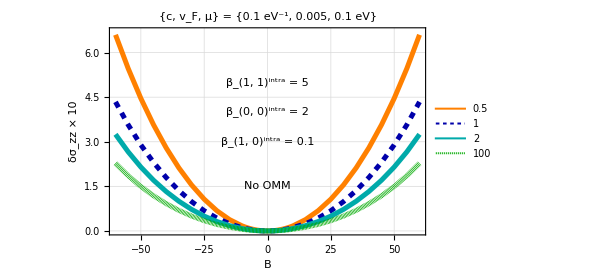

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat11,dat21,dat31,dat41},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{Automatic,6.7}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 5",{0,5}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,4}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,3}],Darker[Brown],16,Bold],(**)Style[Text["No OMM",{0,1.5}],Blue,16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];

leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{FontFamily->"Times",18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
pl=Legended[g1,Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
```

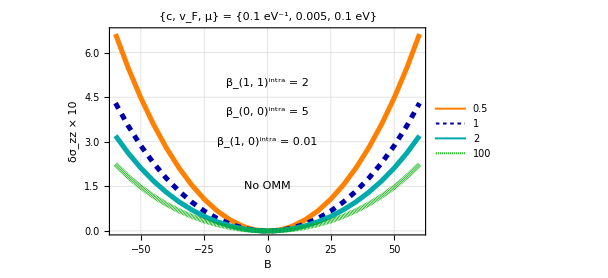

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat51,dat61,dat71,dat81},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{Automatic,6.7}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],PlotTheme->"Detailed",PlotLegends->None,ImageSize->450,Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,5}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 5",{0,4}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.01",{0,3}],Darker[Brown],16,Bold],(**)Style[Text["No OMM",{0,1.5}],Blue,16,Bold]}];


leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
pl=Legended[g1,Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
```

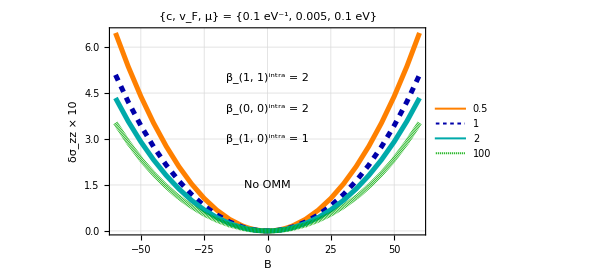

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat91,dat101,dat111,dat121},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{Automatic,6.5}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],PlotTheme->"Detailed",PlotLegends->None,ImageSize->450,Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,5}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,4}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 1",{0,3}],Darker[Brown],16,Bold],(**)Style[Text["No OMM",{0,1.5}],Blue,16,Bold]}];


leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[g1,Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
```

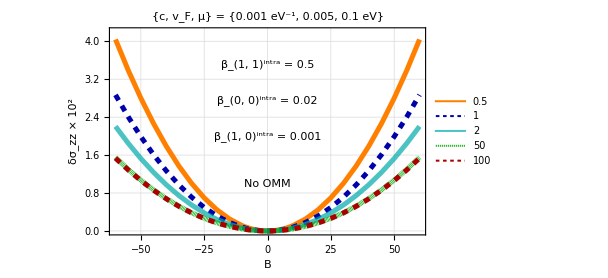

{0.5,1,2,50,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]],Directive[Darker[Red],Thickness[0.008],Dashing[0.01]]};

g1=ListPlot[{d1,d2,d3,d4,d5},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotRange->{{-60,60},{Automatic,4.2}},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None,PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(***)Epilog->{Style[Text["β_(1, 1)^intra = 0.5",{0,3.5}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 0.02",{0,2.75}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.001",{0,2}],Darker[Brown],16,Bold],(**)Style[Text["No OMM",{0,1}],Blue,16,Bold]}(********)];
(* {0.5,0.02,0.001} *)
leg=LineLegend[style,{"0.5","1","2","50","100"},LabelStyle->{FontFamily->"Times",18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[g1,Placed[leg,Below]]
{rat1,rat2,rat3,rat4p,rat5p}
```